```mathematica
ClearAll["Global`*"]
```

# -Graphics-

Plot options and export function

```mathematica
figpath[filename_]:=StringTemplate["/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures/``.pdf"][filename];
export[object_,name_]:=Export[figpath[name],object/. {EdgeForm[],r_?(MemberQ[{RGBColor,Hue,CMYKColor,GrayLevel},Head[#]]&),i___}:>{EdgeForm[r],r,i},ImageResolution->1500];
```

```mathematica
j0=11/2;
theta0=70*π/180;
j1=j0*Cos[theta0];
j2=j0*Sin[theta0];
moi1=10;
moi2=40;
moi3=20;
A1Const=1/(2*moi1);
A2Const=1/(2*moi2);
A3Const=1/(2*moi3);
```

```mathematica
x1[I_,theta_,phi_]:=I*Sin[theta]*Sin[phi];
x2[I_,theta_,phi_]:=I*Cos[theta];
x3[I_,theta_,phi_]:=I*Sin[theta]*Cos[phi];
A[I_]:=A2Const*(1-j2/I)-A1Const;
u[I_]:=(A3Const-A1Const)/A[I];
v0[I_]:=(-A1Const*j1)/A[I];
```

Classical energy function H’

```mathematica
Hprime[I_,theta_,phi_]:=x2[I,theta,phi]^2+u[I]*x3[I,theta,phi]^2+2*v0[I]*x1[I,theta,phi];
```

Minimum points

```mathematica
(*absolute minimum *)
min1=Values@FindMinimum[{Hprime[19/2,x,y],x>1&&x<π&&y>π&&y<2π},{x,y}][[2]];
min2=Values@FindMinimum[{Hprime[19/2,x,y],x>1&&x<π&&y>0.5&&y<2},{x,y}][[2]];
saddle1=Values@FindMaximum[{Hprime[19/2,π/2,y],y>0.1&&y<1},{y}][[2,1]];
saddle2=Values@FindMaximum[{Hprime[19/2,π/2,y],y>2&&y<4},{y}][[2,1]];
```

```mathematica
(* Trick for custom ticks *)
(* source: https://mathematica.stackexchange.com/questions/190490/add-minor-ticks-to-custom-ticks?noredirect=1&lq=1 *)
tickFuncText[x_,y_]:=Join[{#,#,{.03,0}}&/@Subdivide[y,x],{#," ",{.01,0}}&/@Subdivide[##,5*x]]&;
tickFuncMute[x_,y_]:=Join[{#," ",{.03,0}}&/@Subdivide[y,x],{#," ",{.01,0}}&/@Subdivide[##,5*x]]&;
```

The contour plot function definition

```mathematica
cp[I_]:=ContourPlot[
Hprime[I,theta,phi],{theta,0,π},{phi,0,2π},
AspectRatio->Automatic,Contours->16,Frame->True,
FrameStyle->Directive[Black,Thick],PlotRangePadding->None,
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},PlotLegends->BarLegend[Automatic,None,LegendLabel->Style["H'(θ_2,φ_2)\n[MeV]",Italic]],
FrameLabel->{"θ_2 [rad]","φ_2 [rad]"},
FrameTicks->{{Automatic,Automatic},{tickFuncText[3,3],tickFuncMute[3,3]}},
ImageSize->280,
ColorFunction->"BlueGreenYellow"
];
```

The minimum points for the energy function

```mathematica
point1=Graphics[{PointSize[Large],Red,Point[min1],Text[Style["m",19,Red,Bold,FontFamily->"Latin Modern Roman"],{1.2,5}]}];
point2=Graphics[{PointSize[Large],Red,Point[min2],Text[Style["m",19,Red,Bold,FontFamily->"Latin Modern Roman"],{1.2,1.8}]}];
point3=Graphics[{PointSize[Large],Blue,Point[{π/2,saddle1}],Text[Style["s",19,Blue,Bold,FontFamily->"Latin Modern Roman"],{1.9,3}]}];
point4=Graphics[{PointSize[Large],Blue,Point[{π/2,saddle2}],Text[Style["s",19,Blue,Bold,FontFamily->"Latin Modern Roman"],{1.9,0.7}]}];
```

Contour plot

```mathematica
Show[cp[19/2],point1,point2,point3,point4]
export[Show[cp[19/2],point1,point2,point3,point4],"New-Boson-Classical-H-2axis-quantization"];
```

-Graphics-

Energy plot for H’ as function of φ_2

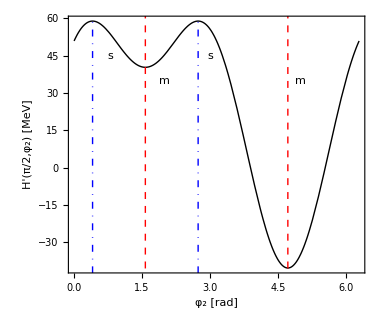

```mathematica
(* sources for adding colored lines inside an Epilog function *)
(* source1: https://mathematica.stackexchange.com/questions/3561/how-to-add-a-vertical-line-to-a-plot *)
(* source2: https://mathematica.stackexchange.com/questions/20218/how-to-color-lines-in-epilog *)
plot1=Plot[
Hprime[19/2,π/2,x],{x,0,2π},
Frame->True,Axes->False,AspectRatio->0.85,ImageSize->380,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
FrameLabel->{"φ_2 [rad]","H'(π/2,φ_2) [MeV]"},
Epilog->{
{Red,Dashed,Thick,Line[{{min1[[2]],-100},{min1[[2]],100}}]},
{Red,Dashed,Thick,Line[{{min2[[2]],-100},{min2[[2]],100}}]},
{Blue,DotDashed,Thick,Line[{{saddle1,-100},{saddle1,100}}]},{Blue,DotDashed,Thick,Line[{{saddle2,-100},{saddle2,100}}]},{Style[Text["s",{0.8,45}],Blue,19,FontFamily->"Latin Modern Roman"]},{Style[Text["s",{3,45}],Blue,19,FontFamily->"Latin Modern Roman"]},
{Style[Text["m",{2,35}],Red,Bold,19,FontFamily->"Latin Modern Roman"]},
{Style[Text["m",{5,35}],Red,Bold,19,FontFamily->"Latin Modern Roman"]}
}
];
Show[plot1]
export[plot1,"New-Boson-Classical-H-2-axis-varphi-plot"];
```